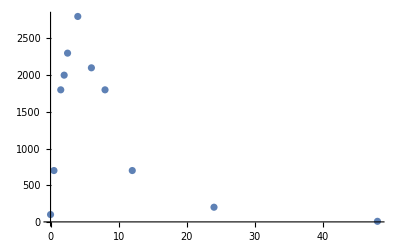

```mathematica
ListPlot[{{0,100},{0.5,700},{1.5,1800},{2,2000},{2.5,2300},{4,2800},{6,2100},{8,1800},{12,700},{24,200},{48,8}}]
```

```mathematica
dataRN = Map[{#[[1]], #[[2]]*10^-3}&,{{0,100},{0.5,700},{1.5,1800},{2,2000},{2.5,2300},{4,2800},{6,2100},{8,1800},{12,700},{24,200},{48,8}} ]
```

{{0,1/10},{0.5,7/10},{1.5,9/5},{2,2},{2.5,23/10},{4,14/5},{6,21/10},{8,9/5},{12,7/10},{24,1/5},{48,1/125}}

```mathematica
nlmRN=NonlinearModelFit[dataRN,{a Exp[c*x]-a Exp[d *x],0>c,0>d},{a,c,d},x,MaxIterations->100000];
```

```mathematica
nlmRN//Normal
```

-1003.01 ⅇ^(-0.267576 x)+1003.01 ⅇ^(-0.265763 x)

```mathematica
nlmRN["BestFitParameters"]
```

{a→1003.01,c→-0.265763,d→-0.267576}

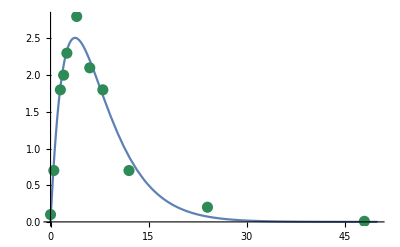

```mathematica
Show[Plot[nlmRN[x],{x,0,50},PlotRange->All],ListPlot[dataRN,PlotStyle->Directive[ColorData["Legacy","SeaGreen"],PointSize[0.02]]]]
```

```mathematica
dataN=Map[{#[[1]], #[[2]]*10^-3}&,{{0,500},{1,700},{2,600},{2.5,500},{4,230},{6,200},{8,100},{11,70},{48,13}}];
```

```mathematica
nlmN=NonlinearModelFit[dataN,{a Exp[c*x]-a Exp[d *x],0>c,0>d},{a,c,d},x,MaxIterations->100000];
```

```mathematica
nlmN//Normal
```

-1.09882 ⅇ^(-2.45523 x)+1.09882 ⅇ^(-0.31842 x)

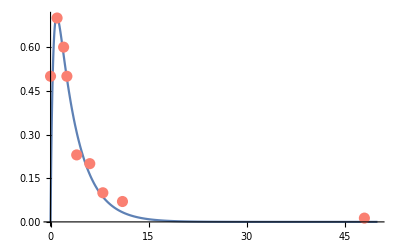

```mathematica
Show[Plot[nlmN[x],{x,0,50},PlotRange->All],ListPlot[dataN,PlotStyle->Directive[ColorData["Legacy","Salmon"],PointSize[0.02]]]]
```

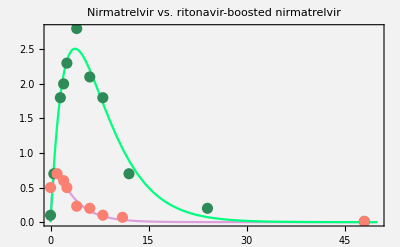

```mathematica
Show[Plot[nlmN[x],{x,0,50},PlotRange->All,PlotStyle->ColorData["Legacy","Plum"],Frame->True, FrameStyle->Directive[ColorData["Legacy","SeaGreen"]],PlotLabel->Style["Nirmatrelvir vs. ritonavir-boosted nirmatrelvir",FontSize->14],Background->Lighter[Gray, 0.9]],
Plot[nlmRN[x],{x,0,50},PlotRange->All,PlotStyle->ColorData["Legacy","SpringGreen"], Frame->True],
ListPlot[dataRN,PlotStyle->Directive[ColorData["Legacy","SeaGreen"],PointSize[0.02]]],ListPlot[dataN,PlotStyle->Directive[ColorData["Legacy","Salmon"],PointSize[0.02]]]]
```